## JIDHUN PP | BSc(Hons) Computer Science| 20211419|Practical-7 Find the Characteristics for the first order PDE and Plotting them Example 1:Find the characteristics of the equation (u-y)u[(x,y),x]+y*u[(x,y),y]=x+y and plot them Solution: The characteristics system is dx/(u-y)=dy/y=du/(x+y) using (i)+(ii)+(iii),we have v=(u+x)/y=c1,is a first integral using (i)+(ii)=(iii),we have w=(x+y)^2-u*u=c2 is a second integral

```mathematica
f0=Plot3D[-x,{x,0,1},{y,0,1},PlotPoints->10]
```

-Graphics3D-

```mathematica
f1=Plot3D[5y-x,{x,0,1},{y,0,1},PlotPoints->10]
```

-Graphics3D-

```mathematica
f2=Plot3D[10y-x,{x,0,1},{y,0,1},PlotPoints->10]
```

-Graphics3D-

```mathematica
g1=Show[f0,f1,f2]
```

-Graphics3D-

```mathematica
h0=Plot3D[x+y,{x,0,1},{y,0,1},PlotPoints->10]
```

-Graphics3D-

```mathematica
h1=Plot3D[Sqrt[(x+y)^2+5],{x,0,1},{y,0,1},PlotPoints->10]
```

-Graphics3D-

```mathematica
h2=Plot3D[Sqrt[(x+y)^2+10],{x,0,1},{y,0,1},PlotPoints->10]
```

-Graphics3D-

```mathematica
g2=Show[ho,h1,h2]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[ho,-Graphics3D-,-Graphics3D-]

```mathematica
Show[GraphicsArray[{g1,g2}]]
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

-Graphics-

### Example 2:The solution of the equation u[(x,y),y]+u[x,y]*u[(x,y),x]=0 can be interpreted as a vector field on the x axis varying with time y.Find the integral satisfying the initial condition u(s,o)=h(s),where h is a given function Solution: We plot the curves {Ct:x=s+t(s^3-3s^2+4) u=s^3-3s^2+4

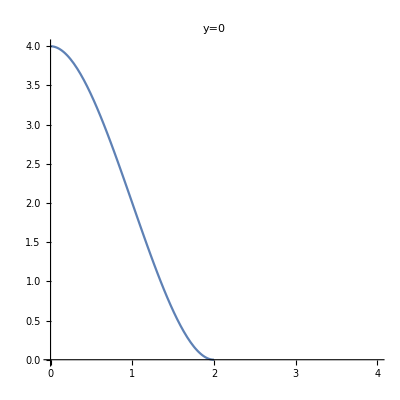

```mathematica
u[s_]:=s^3-3s^2+4;
x[s_,t_]:=s+t*u[s];
ho=ParametricPlot[{x[s,0],u[s]},{s,0,2},PlotRange->{0,4},PlotLabel->"y=0"]
```

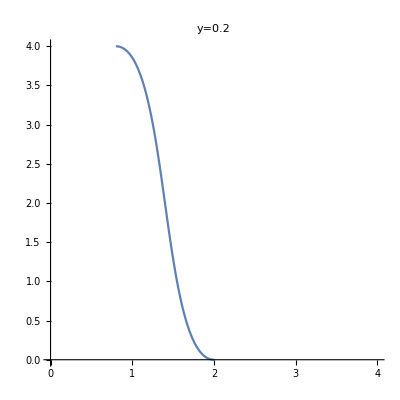

```mathematica
h1=ParametricPlot[{x[s,0.2],u[s]},{s,0,2},PlotRange->{0,4},PlotLabel->"y=0.2"]
```

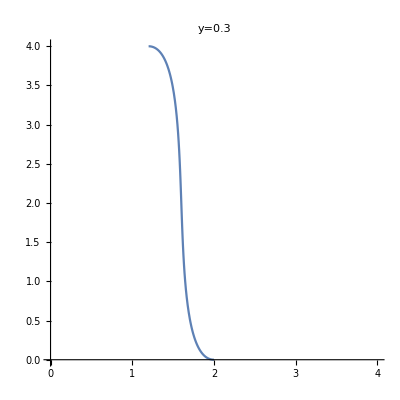

```mathematica
h2=ParametricPlot[{x[s,0.3],u[s]},{s,0,2},PlotRange->{0,4},PlotLabel->"y=0.3"]
```

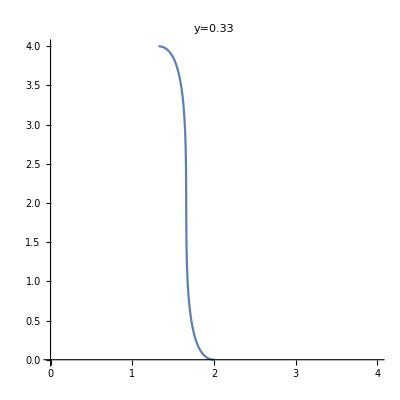

```mathematica
h3=ParametricPlot[{x[s,0.33],u[s]},{s,0,2},PlotRange->{0,4},PlotLabel->"y=0.33"]
```

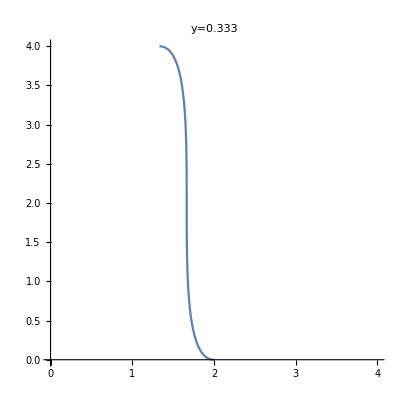

```mathematica
h4=ParametricPlot[{x[s,0.333],u[s]},{s,0,2},PlotRange->{0,4},PlotLabel->"y=0.333"]
```

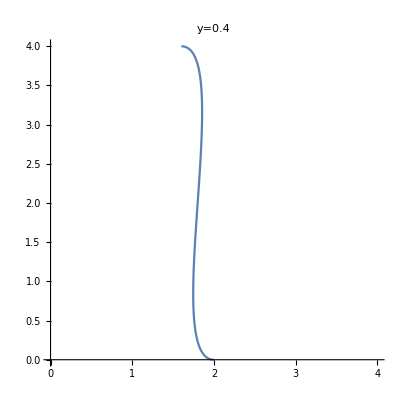

```mathematica
h5=ParametricPlot[{x[s,0.4],u[s]},{s,0,2},PlotRange->{0,4},PlotLabel->"y=0.4"]
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

Show::shx: No graphical objects to show.

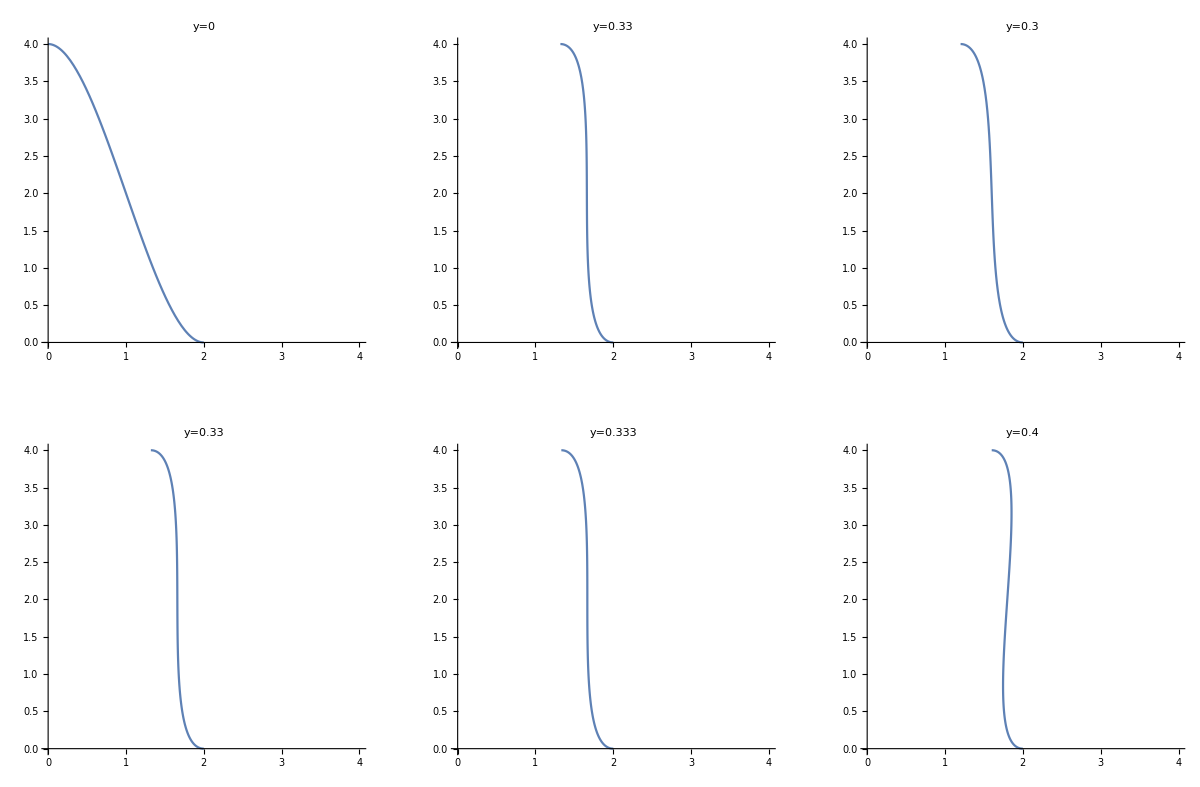
Show[-Graphics-.FrameTicks→None,Frame→False]

Show::shx: No graphical objects to show.

Show[FrameTicks→None,Frame→False]

```mathematica
Show[GraphicsArray[{{ho,h1,h2},{h3,h4,h5}}].FrameTicks->None,Frame->False]
Show[FrameTicks->None,Frame->False]
```